```mathematica
(*
outTimeAndStep
outTimeAndError
*)
SetDirectory[NotebookDirectory[]];
```

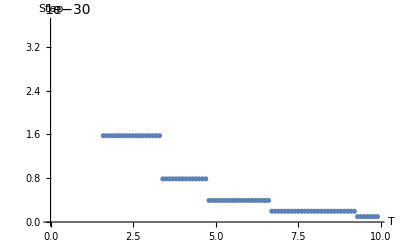

```mathematica
outTimeAndStep=Partition[Delete[ReadList["outTimeAndStep.txt", Real], 1], 2];
Show[ListPlot[{outTimeAndStep},AxesLabel->{"T", "Step"},AxesStyle->Thick,LabelStyle->Directive[20]]]
```

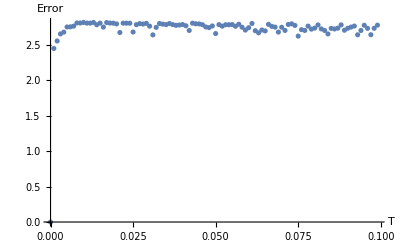

```mathematica
outTimeAndError=Partition[Delete[ReadList["outTimeAndError.txt", Real], 1], 2];
Show[ListPlot[{outTimeAndError},AxesLabel->{"T", "Error"},AxesStyle->Thick,LabelStyle->Directive[20]]]
```

```mathematica
Plot[{Сos[x], -Sin[x]}, {x, 0, 10}];
```